# Vaje za 3. teden

6.  3.  2025

## Naloga 0

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem quick sort

Quicksort[sez_] :=

```mathematica
Quicksort[sez_]:=
If[Length[sez] <= 1, sez,
Module[{sezManjse, sezEnako, sezVecje},
sezManjse = Select[sez, # < First[sez] &];
sezEnako = Select[sez, # == First[sez] &];
sezVecje = Select[sez, # > First[sez] &];
Join[Quicksort[sezManjse], sezEnako, Quicksort[sezVecje]]
]
]

Quicksort[{4,2,5,3,1,5,3,2,4}]
```

{1,2,2,3,3,4,4,5,5}

```mathematica
seznam = Table[RandomInteger[100], 100]
```

```mathematica
{12,92,96,65,89,2,71,5,18,35,80,9,16,82,12,24,78,96,13,21,45,23,79,10,65,90,31,30,24,69,83,64,97,9,87,59,43,61,6,67,19,94,41,46,59,19,4,38,32,50,55,11,60,72,78,39,3,75,57,87,90,100,12,99,93,15,24,47,43,96,25,15,100,52,28,18,70,13,71,60,52,32,21,76,62,65,79,74,12,67,62,79,36,3,29,89,88,67,88,22}

Quicksort[seznam]
```

{12,92,96,65,89,2,71,5,18,35,80,9,16,82,12,24,78,96,13,21,45,23,79,10,65,90,31,30,24,69,83,64,97,9,87,59,43,61,6,67,19,94,41,46,59,19,4,38,32,50,55,11,60,72,78,39,3,75,57,87,90,100,12,99,93,15,24,47,43,96,25,15,100,52,28,18,70,13,71,60,52,32,21,76,62,65,79,74,12,67,62,79,36,3,29,89,88,67,88,22}

{2,3,3,4,5,6,9,9,10,11,12,12,12,12,13,13,15,15,16,18,18,19,19,21,21,22,23,24,24,24,25,28,29,30,31,32,32,35,36,38,39,41,43,43,45,46,47,50,52,52,55,57,59,59,60,60,61,62,62,64,65,65,65,67,67,67,69,70,71,71,72,74,75,76,78,78,79,79,79,80,82,83,87,87,88,88,89,89,90,90,92,93,94,96,96,96,97,99,100,100}

## Naloga 1

Napišite prepisovalno pravilo, ki bo izračunalo produkt dvečlenika z dvočlenikom. S tem pravilom oenostavi izraz (2x - 4)(3 - 4y).

```mathematica
prep = {b_ * (c_ + d_) -> b * c + b * d};
(2x - 4) (3 - 4y) //. prep
```

## Naloga 2

a) Definiraj funkcijo nakljucnaStevila, ki sprejme naravno število n in vrne seznam naključnih celih števil med -100 in 100 dolžine n.
c) S  pomočjo  prepisovalnih  pravil implementiraj urejanje z mehurčki (Bubble sort).

```mathematica
nakljucnaStevila[n_] := Table[RandomInteger[{-100, 100}], n]
```

```mathematica
prep = {a___, b_, c_ , d___} /; b > c -> {a, c, b, d}
```

{a___,b_,c_,d___}/;b>c→{a,c,b,d}

```mathematica
nakljucnaStevila[10] //. prep
```

{-97,-62,-42,-40,12,67,68,85,89,100}

## Naloga 3

- Definiraj funkcijo ZadnjaStevka, ki kot argument sprejme naravno število n in vrne zadnjo števko števila n. (ZadnjaStevka(8138719) vrne 9)
- Definiraj funkcijo PrvaStevka, ki kot argument sprejme naravno število n in vrne prvo števko števila n. (PrvaStevka(8138719) vrne 8)
- Definiraj funkcijo Parabola, ki sprejme koeficiente parabole a, b in c in nariše graf parabole ax^2 + bx + c. Graf naj bo narisan tako, da bo teme parabole vedno vidno na sliki.

## Naloga 4

Definiraj naslednje sezname:
- {1/(2^20), 1/(2^19), ..., 1/2, 1, 2, 4, 8, ..., 2^24}
- {{}, {1}, {2}, {3}, ..., {99}, {99}, {98}, ..., {2}, {1}, {}}
- seznam dolžine 100, v katerem je vsak naslednji element za eno mesto bolj natančen približek števila π. ({3, 3.1, 3.14, ...})

## Naloga 5

Definiraj funkcijo, ki je za pozitivne x enaka sin(x)/x, za x manjši ali enak 0 pa je enaka cos(x). Pomagaj si s funkcijo `Piecewise`.

```mathematica
f[x_] := Piecewise[{{Sin[x] / x, x>0}, {Cos[x], x <= 0}}]
```

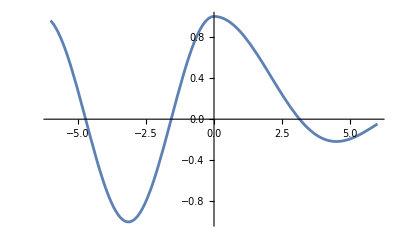

```mathematica
Plot[f[x], {x, -6, 6}]
```

## Naloga 6

Dano je zaporedje  
a) V Mathematici definiraj zaporedje .
b) Definiraj seznam, ki vrne prvih 30 členov zaporedja.
c) Izračunaj limito zaporedja . Izračunaj tudi limito zaporedja . Ali vrsta  konvergira?
d) Izračunaj numerični približek vsote vrste  (uporabi NSum).

```mathematica
a[n_] := Power[(2 n ^ 2 + n + 1) /(2 n ^ 2 - 1), -n^2]
```

```mathematica
prvih30 = Table[a[i], {i , 1, 30}];
```

```mathematica
N /@ Sin /@ prvih30
```

{0.247404,0.163257,0.0980703,0.0589261,0.0354903,0.0214137,0.0129365,0.00782199,0.00473249,0.00286458,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7}

```mathematica
Limit[a[n],n -> Infinity]
```

0

```mathematica
Limit[Power[a[n], 1/n], n -> Infinity]
```

1/(√ⅇ)

## Naloga 7

Dano  je  rekurzivno  zaporedje .

a) V Mathematici definiraj zaporedje  z začetnim členom .
b) Izračunaj prvih 5 členova zaporedja . Nato vse vse izraze razširi in združi na skupni ulomek.

## Naloga 8

Za zaporedje  z začetnima členoma  in  izračunajte njegovo limito. Uporabite RSolveValue.

## Naloga 9

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100.

WolframAlphaQueryResults

### Naloge

Določi 443. števko v decimalnem zapisu števila pi.

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

Izračunaj f(3), kjer je f(x)=1+1/x.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 10

Naslednje naloge reši z vnosom z naravnim jezikom.

### Naloge

Določi površino Slovenije in skupno dolžno njene meje.

Koliko Slovenij prekrije površino Rusije?

Kolikšna je temperatura sonca?